```mathematica
(*Calculate exponents that control the decay speed. Condition: weight decay, different inputs*)
(*w=1*)
q[v_]:=0.5*Erfc[v/(√2)];
(*Int*)
gTmp1[x_, b_, k_, beta_, ns_, w_]:=beta-x/w(k+b-(1-beta/ns)w x);
gTmp2[x_, b_, k_, beta_, ns_, w_]:=k+b-(1-beta/ns)w x;
(*gTmp1[x_, b_, k_, beta_, ns_, w_]:=beta-x/w(k+b-w x);
gTmp2[x_, b_, k_, beta_, ns_, w_]:=k+b-w x;*)
g1Int[b_?NumericQ, k_?NumericQ, nd_?NumericQ, ns_?NumericQ, ndR_?NumericQ, beta_?NumericQ, w_?NumericQ]:=NIntegrate[gTmp1[x, b, k, beta, ns, w] Exp[-x^2/2]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
g1NonInt[b_, k_, nd_, ns_, ndR_, beta_, w_]:=Module[{bk, bla},
bk=b+k;
bla =  Max[Sqrt[2]w InverseErfc[(2ndR)/nd], -100];
1./(2 ns √(2 π) w)(-2 ⅇ^(-bla^2/2) (bk ns+bla (beta-ns) w)+2 bk ⅇ^(-bk^2/2) (ns+beta w-ns w)+(beta (-1+ns)+ns) √(2 π) w (Erf[bk/(√2)]-Erf[bla/(√2)]))
];
g21Int[b_?NumericQ, k_?NumericQ, nd_?NumericQ, ns_?NumericQ, ndR_?NumericQ, beta_?NumericQ, w_?NumericQ]:=NIntegrate[gTmp2[x, b, k, beta, ns, w]^2 Exp[-x^2/2.]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
g21NonInt[b_, k_, nd_, ns_, ndR_, beta_, w_]:=Module[{bk, bla},
bk=b+k;
bla =  Max[Sqrt[2]w InverseErfc[(2ndR)/nd], -100];
1./(2 ns^2 √(2 π))(-2 bk ⅇ^(-bk^2/2) (beta-ns) w (-ns (-2+w)+beta w)+2 ⅇ^(-bla^2/2) (beta-ns) w (2 bk ns+bla (beta-ns) w)+√(2 π) (bk^2 ns^2+(beta-ns)^2 w^2) Erf[bk/(√2)]-√(2 π) (bk^2 ns^2+(beta-ns)^2 w^2) Erf[bla/(√2)])
];
g22Int[b_?NumericQ, k_?NumericQ, nd_?NumericQ, ns_?NumericQ, ndR_?NumericQ, beta_?NumericQ, w_?NumericQ]:=NIntegrate[(gTmp1[x, b, k, beta, ns, w]^2-gTmp2[x, b, k, beta, ns, w]^2/w^2) Exp[-x^2/2]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
g22NonInt[b_, k_, nd_, ns_, ndR_, beta_, w_]:=Module[{bk, bla},
bk=b+k;
bla =  Max[Sqrt[2]w InverseErfc[(2ndR)/nd], -100];
1./(ns^2 √(2 π) w^2)(ⅇ^(-bla^2/2) (bk ns+bla (beta-ns) w) (bk bla ns+beta (2+bla^2-2 ns) w-(2+bla^2) ns w)+bk ⅇ^(-bk^2/2) (ns+beta w-ns w) (2 (beta (-1+ns)+ns) w+bk^2 (ns (-1+w)-beta w))+(2 beta^2-2 beta (2+beta) ns+(2+beta (2+beta)) ns^2) √(π/2) w^2 Erf[bk/(√2)]-(2 beta^2-2 beta (2+beta) ns+(2+beta (2+beta)) ns^2) √(π/2) w^2 Erf[bla/(√2)])
];
g31Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=NIntegrate[3gTmp1[x, b, k, beta, ns, w] gTmp2[x, b, k, beta, ns, w]^2 Exp[-x^2/2]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
g31NonInt[b_, k_, nd_, ns_, ndR_, beta_, w_]:=Module[{bk, bla},
bk=b+k;
bla =  Max[Sqrt[2]w InverseErfc[(2ndR)/nd], -100];
1./(2 ns^3 √(2 π) w)3 (ⅇ^(-bk^2/2) (2 bk^3 ns^3+6 bk^3 (beta-ns) ns^2 w-2 bk (beta-ns) ns (2 beta (-3+ns)+6 ns+3 bk^2 (-beta+ns)) w^2-2 bk (beta-ns)^2 ((3+bk^2) ns+beta (-3-bk^2+ns)) w^3)+ⅇ^(-bla^2/2) (-2 bk^3 ns^3-6 bk^2 bla (beta-ns) ns^2 w+2 bk (beta-ns) ns (2 beta (-3+ns)+6 ns+3 bla^2 (-beta+ns)) w^2+2 bla (beta-ns)^2 ((3+bla^2) ns+beta (-3-bla^2+ns)) w^3)+(beta (-3+ns)+3 ns) √(2 π) w (bk^2 ns^2+(beta-ns)^2 w^2) Erf[bk/(√2)]-(beta (-3+ns)+3 ns) √(2 π) w (bk^2 ns^2+(beta-ns)^2 w^2) Erf[bla/(√2)])
];
g32Int[b_, k_, nd_, ns_, ndR_, beta_, w_]:=NIntegrate[(gTmp1[x, b, k, beta, ns, w]^3-1/w^2 3gTmp1[x, b, k, beta, ns, w] gTmp2[x, b, k, beta, ns, w]^2) Exp[-x^2/2]/(√(2.π))Sum[Binomial[nd-1, m-1] q[x]^(m-1)(1-q[x])^(nd-m), {m, 1, ndR}], {x, -Infinity, k+b}];
g32NonInt[b_, k_, nd_, ns_, ndR_, beta_, w_]:=Module[{bk, bla},
bk=b+k;
bla =  Max[Sqrt[2]w InverseErfc[(2ndR)/nd], -100];
1./(ns^3 √(2 π) w^3)(-ⅇ^(-bla^2/2) (bk ns+bla (beta-ns) w) (bk^2 (-1+bla^2) ns^2+bk bla ns (beta+2 bla^2 (beta-ns)-ns-3 beta ns) w+6 beta^2 w^2+(bla^4 (beta-ns)^2+3 ns (beta (2+beta) (-2+ns)+2 ns)+bla^2 (-beta+ns) (2 ns+beta (-2+3 ns))) w^2)-bk ⅇ^(-bk^2/2) (ns (-1+w)-beta w) (3 (2 beta (-2+ns) ns+2 ns^2+beta^2 (2-2 ns+ns^2)) w^2+bk^4 (ns (-1+w)-beta w)^2+bk^2 (2 beta^2 w^2+ns^2 (-1+w) (1+(2+3 beta) w)+beta ns w (1-(4+3 beta) w)))+(-6 beta^3+6 beta^2 (3+beta) ns-3 beta (6+beta (4+beta)) ns^2+(6+beta (6+beta (3+beta))) ns^3) √(π/2) w^3 Erf[bk/(√2)]-(-6 beta^3+6 beta^2 (3+beta) ns-3 beta (6+beta (4+beta)) ns^2+(6+beta (6+beta (3+beta))) ns^3) √(π/2) w^3 Erf[bla/(√2)])
];
(*betaSolution[b_, k_, nd_, ns_, ndR_, w_]:=y/.FindRoot[g21Int[b, k, nd, ns, ndR, y, w]-2g1Int[b, k, nd, ns, ndR, y, w]+g22Int[b, k, nd, ns, ndR, y, w]/ns , {y, 0., 40.}, Method->"Brent"];*)
betaSolution[b_, k_, nd_, ns_, ndR_, w_]:=y/.FindRoot[g21Int[b, k, nd, ns, ndR, y, w]-2g1Int[b, k, nd, ns, ndR, y, w] , {y, -10, 100.}, Method->"Brent"];
betaSolutionNonInt[b_, k_, nd_, ns_, ndR_, w_]:=y/.FindRoot[g21NonInt[b, k, nd, ns, ndR, y, w]-2g1NonInt[b, k, nd, ns, ndR, y, w]+g22NonInt[b, k, nd, ns, ndR, y, w]/ns, {y,10}];
(*betaSolutionNonInt[b_, k_, nd_, ns_, ndR_, w_]:=y/.FindRoot[g21NonInt[b, k, nd, ns, ndR, y, w]-2g1NonInt[b, k, nd, ns, ndR, y, w], {y,10}];*)
```

```mathematica
(*****************************************************************************)
```

```mathematica
tmpfunInt[b_, bk_, ndR_, nd_, ns_]:=Module[{k, beta, g1, g21, g22, g31, g32}, 
k = bk-b;
beta = betaSolution[b, k, nd, ns, ndR, 1.]//Quiet; 
g1 = g1Int[b, k, nd, ns, ndR, beta, 1.]//Quiet;
g21 = g21Int[b, k, nd, ns, ndR, beta, 1.]//Quiet;
g22 = g22Int[b, k, nd, ns, ndR, beta, 1.]//Quiet;
g31 = g31Int[b, k, nd, ns, ndR, beta, 1.]//Quiet;
g32 = g32Int[b, k, nd, ns, ndR, beta, 1.]//Quiet;
{beta, g1, g21, g22, g31, g32}
];
tmpfunNonInt[b_, bk_, ndR_, nd_, ns_]:=Module[{k, beta, g1, g21, g22, g31, g32}, 
k = bk-b;
beta = betaSolutionNonInt[b, k, nd, ns, ndR, 1.]//Quiet; 
g1 = g1NonInt[b, k, nd, ns, ndR, beta, 1.]//Quiet;
g21 = g21NonInt[b, k, nd, ns, ndR, beta, 1.]//Quiet;
g22 = g22NonInt[b, k, nd, ns, ndR, beta, 1.]//Quiet;
g31 = g31NonInt[b, k, nd, ns, ndR, beta, 1.]//Quiet;
g32 = g32NonInt[b, k, nd, ns, ndR, beta, 1.]//Quiet;
{beta, g1, g21, g22, g31, g32}
];
```

```mathematica
paramsList = Import["/home/fangxu/BennaLab/dendrite_familiarity_detection/tmp_data/tmp.csv"];
paramsList//Dimensions
```

{2,5}

```mathematica
paramsFunTmp[nd_, ns_, b_, bk_, ndR_]:=Module[{beta}, 
beta = betaSolution[0., bk, nd, ns, ndR, 1.]//Quiet;
{nd, ns, bk, b, ndR, beta, 20240305}
];
(*paramsFunTmp[nd_, ns_, b_, bk_, ndR_]:=Module[{beta}, 
beta = betaSolutionNonInt[0., bk, nd, ns, ndR, 1.]//Quiet;
{nd, ns, bk, b, ndR, beta, 20240305}
];*)
tmpParams = ParallelTable[paramsFunTmp[paramsList[[idx, 4]],paramsList[[idx, 5]], paramsList[[idx, 1]], paramsList[[idx, 2]], paramsList[[idx, 3]]], {idx, 1, Length[paramsList]}];
```

```mathematica
Export["/home/fangxu/BennaLab/dendrite_familiarity_detection/tmp_data/params_list_tmp2.csv", tmpParams, "CSV"];
```

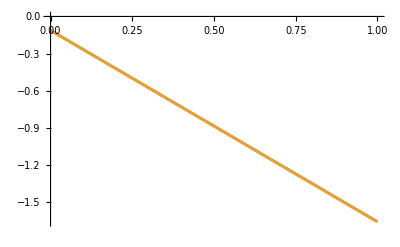

```mathematica
Clear["tmpfun"]
tmpfun2[y_, bk_, nd_, ns_, ndR_]:=g21Int[0.,bk,nd,ns,ndR,y,1.]-2 g1Int[0.,bk,nd,ns,ndR,y,1.]+1/ns g22Int[0.,bk,nd,ns,ndR,y,1.];
tmpfun1[y_, bk_, nd_, ns_, ndR_]:=g21Int[0.,bk,nd,ns,ndR,y,1.]-2 g1Int[0.,bk,nd,ns,ndR,y,1.];
nd=1500;ns=40;bk=7.5;ndR=60;
Plot[{tmpfun2[y, bk, nd, ns, ndR], tmpfun1[y, bk, nd, ns, ndR]}, {y, 0, 1}]
```

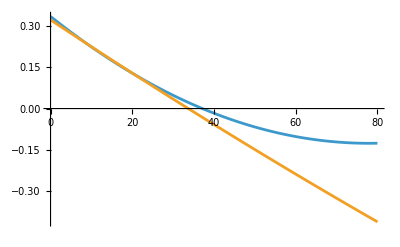

```mathematica
Clear["tmpfun"]
tmpfun2[y_, bk_, nd_, ns_, ndR_]:=g21NonInt[0.,bk,nd,ns,ndR,y,1.]-2 g1NonInt[0.,bk,nd,ns,ndR,y,1.]+1/ns g22NonInt[0.,bk,nd,ns,ndR,y,1.];
tmpfun1[y_, bk_, nd_, ns_, ndR_]:=g21NonInt[0.,bk,nd,ns,ndR,y,1.]-2 g1NonInt[0.,bk,nd,ns,ndR,y,1.];
nd=750;ns=80;bk=7.5;ndR=5;
Plot[{tmpfun2[y, bk, nd, ns, ndR], tmpfun1[y, bk, nd, ns, ndR]}, {y, 0, 80}]
```

```mathematica
paramsList
```

{{2.3,6.5,1,3,20000},{2.3,6.75,1,3,20000},{2.3,7.,1,3,20000},{2.6,5.25,1,4,15000},{2.6,5.,1,4,15000},{2.6,4.75,1,4,15000},{2.6,4.5,1,4,15000},{0.95,4.,2,4,15000},{0.95,3.75,2,4,15000},{2.45,6.,1,5,12000},{2.45,6.25,1,5,12000},{2.45,6.5,1,5,12000},{2.45,6.75,1,5,12000},{0.65,3.25,3,5,12000},{0.65,3.,3,5,12000},{2.9,6.25,1,10,6000},{2.9,6.5,1,10,6000},{2.9,6.75,1,10,6000},{2.9,7.,1,10,6000},{0.8,3.,4,10,6000},{0.8,2.75,4,10,6000},{3.05,5.25,1,15,4000},{3.05,5.,1,15,4000},{3.05,4.75,1,15,4000},{3.05,4.5,1,15,4000},{1.4,3.5,3,15,4000},{1.4,3.25,3,15,4000},{1.1,4.25,4,15,4000},{0.95,4.,5,15,4000},{1.4,4.25,4,20,3000},{1.4,4.5,4,20,3000},{1.4,4.75,4,20,3000},{3.35,5.5,1,30,2000},{3.35,5.25,1,30,2000},{3.35,5.,1,30,2000},{3.35,4.75,1,30,2000},{2.,4.5,2,30,2000},{2.,4.25,2,30,2000},{2.,4.,2,30,2000},{2.,3.75,2,30,2000},{1.55,4.5,4,30,2000},{1.4,4.,5,30,2000},{1.4,4.25,5,30,2000},{1.7,3.25,5,50,1200},{3.35,6.75,1,60,1000},{3.35,7.,1,60,1000},{3.35,7.25,1,60,1000},{3.35,7.5,1,60,1000},{2.,3.75,4,75,800},{1.85,4.5,5,75,800},{2.6,4.5,2,100,600},{2.6,4.25,2,100,600},{2.3,5.,3,100,600},{2.45,5.25,3,150,400},{2.9,6.,2,300,200},{2.75,5.75,3,300,200},{3.05,6.,2,400,150},{3.05,6.25,2,400,150},{3.05,6.5,2,400,150},{2.9,5.5,3,400,150},{4.1,6.25,1,1000,60},{4.1,6.5,1,1000,60},{4.1,6.75,1,1000,60},{4.1,7.,1,1000,60},{3.2,5.5,3,1000,60},{3.2,5.75,3,1000,60},{3.2,6.,3,1000,60},{2.6,4.75,10,1000,60},{3.35,5.5,2,1500,40},{3.35,5.75,2,1500,40}}